```mathematica
uif =NDSolveValue[{-Laplacian[u[x,y],{x,y}]==1, u[x,0]== 0,u[x,1]==1,
u[0,y]==0, u[1,y]==0},{x,0,1},{y,0,1}]
```

NDSolveValue::noout: No functions were specified for output from NDSolveValue.

NDSolveValue::underdet: There are more dependent variables, {u[0,y],u[1,y],u[x,y],u^(2,0)[x,y]}, than equations, so the system is underdetermined.

NDSolveValue[{-u^(0,2)[x,y]-u^(2,0)[x,y]==1,u[x,0]==0,u[x,1]==1,u[0,y]==0,u[1,y]==0},{x,0,1},{y,0,1}]

```mathematica
Clear[u]
```

```mathematica
eqn=-∇_{x,y} .(1/(√(1+(∇_{x,y} u[x,y])^2)))∇_{x,y} u[x,y] ==0;
```

```mathematica
usol = NDSolveValue[{eqn, DirichletCondition[u[x,y] == Sin[2 π *(x+y)],True]},u[x,y],{x,y} ∈ Disk[],InitialSeeding->{u[x,y]==0}]
```

Thread::tdlen: Objects of unequal length in {(u$23054^2 u$23055)/((1+u$23054^2)^(3/2)),(u$23053 u$23054)/((1+u$23053^2)^(3/2)),(u$23053 u$23054 u$23056)/((1+u$23053^2)^(3/2)),u$23054^2/((1+u$23054^2)^(3/2))} {u$23056,u$23055} cannot be combined.

Div::sclr: The scalar expression … does not have a divergence.

Thread::tdlen: Objects of unequal length in {u^(2,0)[x,y],u^(0,2)[x,y]} {((u^(0,1)[x,y])^2 u^(0,2)[x,y])/((1+(u^(0,1)[x,y])^2)^(3/2)),(u^(0,1)[x,y] u^(1,0)[x,y])/((1+(u^(1,0)[x,y])^2)^(3/2)),(u^(0,1)[x,y] u^(1,0)[x,y] u^(2,0)[x,y])/((1+(u^(«1»)[x,y])^2)^(3/2)),((u^(0,1)[x,y])^2)/((1+(u^(0,1)[x,y])^2)^(3/2))} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Div::sclr: The scalar expression 1/2 (NDSolve`FEM`PDEParserDump`makeKappaMatrix[{1/(√2),1/(2 √2),1/(√2),1/(2 √2)},{{2,0},{0,2}},2]+Transpose[NDSolve`FEM`PDEParserDump`makeKappaMatrix[{1/(√2),1/(2 √2),1/(√2),1/(2 √2)},{{2,0},{0,2}},2]]) does not have a divergence.

General::stop: Further output of Div::sclr will be suppressed during this calculation.

NDSolveValue::femnlmdor: The maximum derivative order of the nonlinear PDE coefficients for the Finite Element Method is larger than 1. It may help to rewrite the PDE in inactive form.

NDSolveValue[{{u^(1,0)[x,y] ((u^(0,1)[x,y] u^(0,2)[x,y])/((1+(u^(0,1)[x,y])^2)^(3/2))+(u^(1,0)[x,y] u^(2,0)[x,y])/((1+(u^(1,0)[x,y])^2)^(3/2))),u^(0,1)[x,y] ((u^(0,1)[x,y] u^(0,2)[x,y])/((1+(u^(0,1)[x,y])^2)^(3/2))+(u^(1,0)[x,y] u^(2,0)[x,y])/((1+(u^(1,0)[x,y])^2)^(3/2)))}==0,DirichletCondition[u[x,y]==Sin[2 π (x+y)],True]},u[x,y],{x,y}∈Disk[{0,0}],InitialSeeding→{u[x,y]==0}]

```mathematica
n=1000;
A=SparseArray[{{i_,i_}->-2.,{i_,j_}/;Abs[i-j]==1->1.},{n,n},0.];
g[x_?VectorQ]:=n^2 A.x+x-x^3-1;
jacobian[x_?VectorQ]:= Module[{d=1-3 x^2},n^2A+SparseArray[{i_,i_}:>d[[i]],{n,n}]]
x0=ConstantArray[0.,n];
```

```mathematica
monitoredFindRoot[args__, jac_]:= Module[{s=0, e=0,j=0},
FindRoot[args, StepMonitor:> s++, EvaluationMonitor:>e++, Jacobian->{jac,EvaluationMonitor:>j++}];
{"Steps"->s," Function Evaluations (g) "->e, " Jacobian Evaluations g(')" ->j}]
```

```mathematica
monitoredFindRoot[g[x],{x,x0},jacobian[x]]
```

{Steps→3, Function Evaluations (g) →4, Jacobian Evaluations g(')→3}

```mathematica
monitoredFindRoot[g[x],{x,x0},Method->{"AffineCovariantNewton"(*,"BroydenUpdates"->False*)},
jacobian[x]]
```

{Steps→5, Function Evaluations (g) →6, Jacobian Evaluations g(')→1}

## Nonlinear diffusion ∂/∂x(-u(x)^2(∂u)/(∂x))+4 = 0

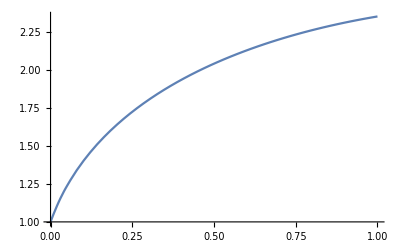

```mathematica
ufun=NDSolveValue[{Div[{{-u[x]^2}}.Grad[u[x],{x}],{x}]==4+NeumannValue[2.,x==1],
DirichletCondition[u[x]==1,x==0]},u,{x}∈ Line[{{0},{1}}],InitialSeeding->{u[x]==1}];
Plot[ufun[x],{x,0,1}]
```

### The solution of the equations u_t-∇^2 f=0

```mathematica
nsolT=NDSolveValue[{D[u[x,t],t]==Div[{{Sqrt[u[x,t]]^2}}.Grad[u[x,t],{x}],{x}],DirichletCondition[u[x,t]==0,x==0],DirichletCondition[u[x,t]==0,x==1], u[x,0]==Sin[x]},u[x,t],{x,0,1},{t,0,10}];
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

```mathematica
NDSolveValue::femcscd: "The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help."
```

```mathematica
Plot3D[nsolT[x,t],{x,0,1},{t,0,3}]
```

-Graphics3D-

```mathematica
op = Div[{{-Derivative[1][u][x]}}.Grad[u[x],{x}],{x}]
```

-2 u'[x] u''[x]

```mathematica
NDSolveValue[{op==4+NeumannValue[2.,x==1],DirichletCondition[u[x]==1.,x==0]},u,{x}∈Line[{{0},{1}}]];
```

NDSolveValue::femnlmdor: The maximum derivative order of the nonlinear PDE coefficients for the Finite Element Method is larger than 1. It may help to rewrite the PDE in inactive form.

```mathematica
NDSolveValue[{op==4+NeumannValue[2.,x==1],DirichletCondition[u[x]==1.,x==0]},u,{x}∈Line[{{0},{1}}]];
```

```mathematica
NDSolveValue[{Inactive[Div][{{-Derivative[1][u][x]}}.Inactive[Grad][u[x],{x}],{x}]==4+NeumannValue[2.,x==1],DirichletCondition[u[x]==1.,x==0]},u,{x}∈Line[{{0},{1}}]];
```

FindRoot::nosol: Linear equation encountered that has no solution.

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

```mathematica
ufun1=NDSolveValue[{Div[{{-1}}.Grad[u[x],{x}],{x}]-2 u[x]D[u[x],x]==0,
DirichletCondition[u[x]==1,x==0],DirichletCondition[u[x]==1/2,x==1]},u,{x}∈Line[{{0},{1}}],
InitialSeeding->{u[x]==1}];
```

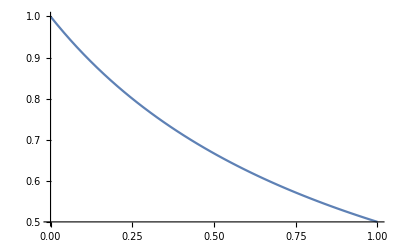

```mathematica
Plot[ufun1[x],{x,0,1}]
```

### Complex valued Nonlinear Reaction

(-∂^2 u)/(∂x^2)+𝒾 u^2=0

```mathematica
ufun2= NDSolveValue[{Div[{{-1}}.Grad[u[x],{x}],{x}]+ⅈ u[x]^2==0,DirichletCondition[u[x]==-6ⅈ,x==0],DirichletCondition[u[x]==Sqrt[2]ⅈ,x==1]},u,{x}∈Line[{{0},{1}}],InitialSeeding->{u[x]==1}];
```

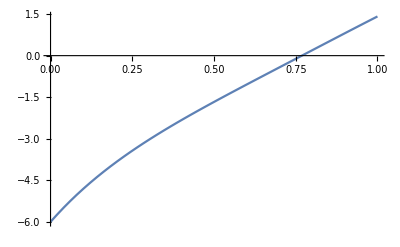

```mathematica
Plot[Im[ufun2[x]],{x,0,1}]
```

### Nonlinear Load

(∂^2 u)/(∂x^2)=sin(u)

```mathematica
ufun3=NDSolveValue[{Div[{{1}}.Grad[u[x],{x}],{x}]==Sin[u[x]],DirichletCondition[u[x]==5,x==0],DirichletCondition[u[x]==6.2,x==1]},u,{x}∈Line[{{0},{1}}],InitialSeeding->{u[x]==1}];
```

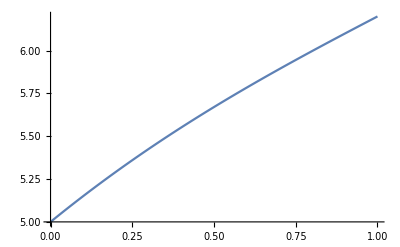

```mathematica
Plot[ufun3[x],{x,0,1}]
```

### Radiation Boundary Condition

u^4-(T^4)_∞

```mathematica
length=4/10;
parameters = {Subscript[T, 0]->500, Subscript[T, ∞]->100, k->40,σ->5675/1000*10^-8,ϵ->35/100,Ar->π radius^2, radius->5/1000};
Clear[u,A];
```

```mathematica
nsol = NDSolveValue[{-k*Ar*D[u[x],{x,2}]==NeumannValue[-ϵ*σ*Ar*(u[x]^4-Subscript[T, ∞]^4),x==length],DirichletCondition[u[x]==500.,x==0]}//.parameters,u,{x,0,length}(*∈ Line[{{0},{length}}]*),Method->"FiniteElement"];
```

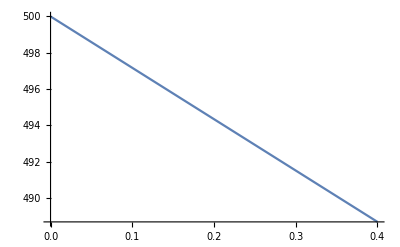

```mathematica
Plot[nsol[x],{x,0,length}]
```

### Nonlinear Robin Boundary Conditions

```mathematica
Ω = RegionUnion[Rectangle[{0,0},{1/2,1}],Disk[{1/2,1/2},1/2]];
```

```mathematica
eqn={∇_{x,y} .(-∇_{x,y} u[x,y])+v[x,y]==Exp[-(x^2+(y-0.5)^2)],
∇_{x,y} .(-∇_{x,y} v[x,y])+u[x,y]==NeumannValue[-u[x,y]^4,x≥1/2]};
```

```mathematica
{nusol,nvsol}=NDSolveValue[{eqn,DirichletCondition[u[x,y]==0,x ==0]},{u,v},{x,y} ∈ Ω,
InitialSeeding->{u[x,y]==1, v[x,y]==1}]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

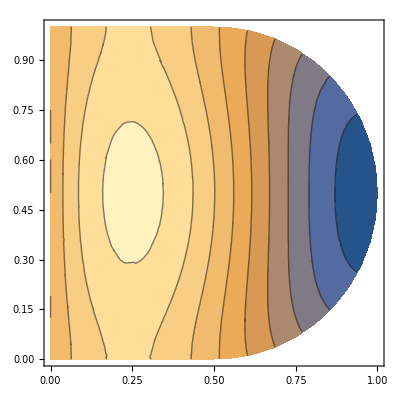

```mathematica
ContourPlot[{nusol[x,y](*,nvsol[x,y]*)},{x,y}∈ Ω]
```

### Magnetostatics I

∇(-1/μ(X,∇_X u)∇u)=j_z

```mathematica
(* find BHdata for some material *)
```

```mathematica
fit=Module[{a1,a2,b1,b2,c1,c2,model,fitData},
model=a1 Exp[-(x-b1)^2/(c1^2)]+a2 / (1+Exp[]]
```

### Burgers' Equation

```mathematica
ufunB = NDSolveValue[{D[u[t,x],t]== 1/100 D[u[t,x],x,x]+u[t,x] D[u[t,x],x],u[t,0]==1,
u[t,1]==1,u[0,x]==Cos[2 Pi x]},u,{t,0,2},{x,0,1}, 
Method->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.01}}}];
```

```mathematica
Plot3D[ufunB[t,x],{t,0,1},{x,0,1}]
```

-Graphics3D-